```mathematica
(* Binomial[n,m] = Subscript[C, n]^m=(n/m)=(n!)/(m!(n-m)!) *)
Binomial[4,3]
```

4

```mathematica
Binomial[10,4]
```

210

```mathematica
(* 用抛硬币举例时，英文用法：正面 Head(H),反面 Tail(T) *)

PDF[BinomialDistribution[n,p],m](* PDF 概率密度函数 *)
```

Piecewise[{{(1-p)^(-m+n) p^m Binomial[n,m], 0≤m≤n}, {0, True}}]

```mathematica
n=100;
p=0.31;
binomialdist=Table[{m,PDF[BinomialDistribution[n,p],m]},{m,0,n}]
```

{{0,7.67201×10^-17},{1,3.44684×10^-15},{2,7.66548×10^-14},{3,1.12501×10^-12},{4,1.22569×10^-11},{5,1.05729×10^-10},{6,7.52108×10^-10},{7,4.53756×10^-9},{8,2.36989×10^-8},{9,1.08839×10^-7},{10,4.44979×10^-7},{11,1.6357×10^-6},{12,5.45034×10^-6},{13,0.0000165758},{14,0.0000462785},{15,0.000119206},{16,0.000284519},{17,0.000631617},{18,0.00130849},{19,0.00253714},{20,0.0046165},{21,0.00790125},{22,0.0127471},{23,0.0194219},{24,0.0279952},{25,0.0382358},{26,0.0495531},{27,0.0610171},{28,0.0714708},{29,0.0797216},{30,0.0847668},{31,0.0859953},{32,0.0833079},{33,0.0771248},{34,0.0682814},{35,0.0578483},{36,0.0469261},{37,0.0364674},{38,0.0271628},{39,0.0194006},{40,0.0132922},{41,0.00873931},{42,0.00551559},{43,0.00334245},{44,0.00194536},{45,0.00108765},{46,0.000584258},{47,0.000301587},{48,0.00014961},{49,0.0000713313},{50,0.0000326884},{51,0.0000143981},{52,6.09552×10^-6},{53,2.48021×10^-6},{54,9.69852×10^-7},{55,3.64429×10^-7},{56,1.31568×10^-7},{57,4.5629×10^-8},{58,1.51983×10^-8},{59,4.86076×10^-9},{60,1.49228×10^-9},{61,4.39634×10^-10},{62,1.24245×10^-10},{63,3.36692×10^-11},{64,8.74515×10^-12},{65,2.17605×10^-12},{66,5.18449×10^-13},{67,1.18201×10^-13},{68,2.57715×10^-14},{69,5.36974×10^-15},{70,1.06839×10^-15},{71,2.02817×10^-16},{72,3.67015×10^-17},{73,6.32457×10^-18},{74,1.03675×10^-18},{75,1.61473×10^-19},{76,2.38638×10^-20},{77,3.34174×10^-21},{78,4.42709×10^-22},{79,5.53894×10^-23},{80,6.53234×10^-24},{81,7.24647×10^-25},{82,7.5436×10^-26},{83,7.34997×10^-27},{84,6.68294×10^-28},{85,5.65173×10^-29},{86,4.42881×10^-30},{87,3.2019×10^-31},{88,2.12511×10^-32},{89,1.28732×10^-33},{90,7.06884×10^-35},{91,3.48995×10^-36},{92,1.53386×10^-37},{93,5.92797×10^-39},{94,1.9833×10^-40},{95,5.62768×10^-42},{96,1.31686×10^-43},{97,2.43973×10^-45},{98,3.35544×10^-47},{99,3.04549×10^-49},{100,1.36826×10^-51}}

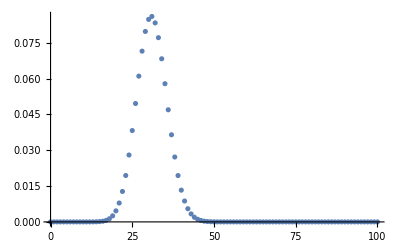

```mathematica
ListPlot[binomialdist,PlotRange->Full]
```

```mathematica
n=1000000;
p=0.5;
binomialdist2=Table[{m,PDF[BinomialDistribution[n,p],m]},{m,0,n}];
ListPlot[binomialdist2,PlotRange->Full]
```

-Graphics-

```mathematica
(* n->∞,Binomial distribution-> P(m)=1/(√(2π)σ)ⅇ^((-(m-np)^2)/(2 σ^2)) (Normal/Gaussian Distribution,离散高斯分布), 
mean=np, standard deviation σ=√(np(1-p)) *)
```

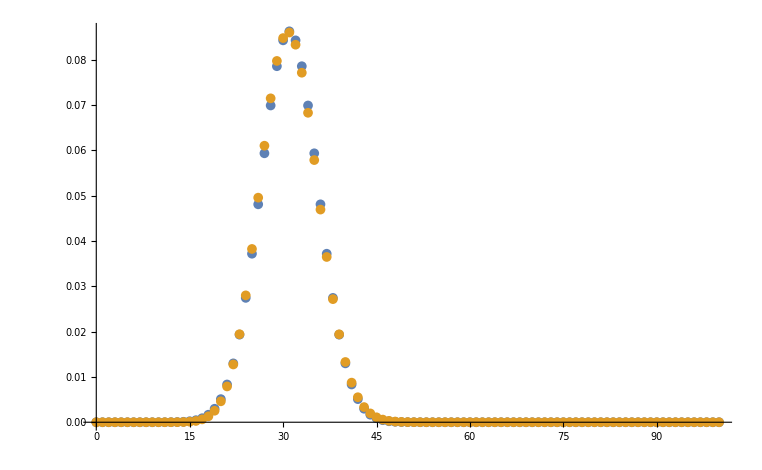

```mathematica
g[m_]:=1/(√(2π) σ) ⅇ^((-(m-n p)^2)/(2 σ^2));
σ=√(n p (1-p));
gaussdist=Table[{m,g[m]},{m,0,n}];
n=100;
p=0.31;
ListPlot[{gaussdist,binomialdist},PlotRange->All]
```

```mathematica
(* Continuous Gaussian distribution
P(x)=1/(√(2π)σ)ⅇ^((-(x-Subscript[x, 0])^2)/(2 σ^2))
mean=Subscript[x, 0] *)
```

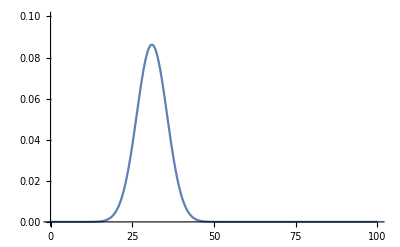

```mathematica
mean=31;
continudist=Plot[PDF[NormalDistribution[mean,σ],x],{x,0,100},PlotRange->{{0,100},{0,0.1}}]
```

```mathematica
Clear[n,p];
PDF[BinomialDistribution[n,p],m]
```

Piecewise[{{(1-p)^(-m+n) p^m Binomial[n,m], 0≤m≤n}, {0, True}}]

```mathematica
Mean[BinomialDistribution[n,p]]
```

n p

```mathematica
StandardDeviation[BinomialDistribution[n,p]]
```

√(n (1-p) p)

```mathematica
Clear[μ,σ,x];
PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
Mean[NormalDistribution[μ,σ]]
```

μ

```mathematica
StandardDeviation[NormalDistribution[μ,σ]]
```

σ

```mathematica
Clear[μ,σ,x];
```

```mathematica
Integrate[x/(√(2 π) σ) ⅇ^((-(x-μ)^2)/(2 σ^2)),{x,-∞,∞},Assumptions->σ≥0](* 算了一下正态分布的期望/均值 *)
```

μ

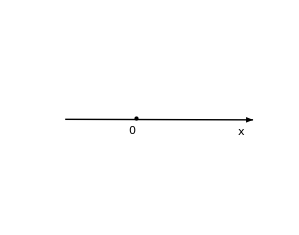

```mathematica
(* 假设0处有一块体积不计的方糖，数轴表示一维的溶剂；
t=0, no diffusion, t=∞, difussion completed;
经证明，P(x,t)=1/(√(2π)σ)ⅇ^(-x^2/(2 σ^2)),σ=2Dt. *)
Clear[σ,d,t,p];
d=1;σ[t_]:=√(2 d t);
p[x_,t_]:=1/(√(2 π) σ[t]) ⅇ^(-x^2/(2 σ[t]^2));
Animate[Plot[p[x,t],{x,-10,10},PlotRange->{0,0.3},PlotStyle->{Thick,Black},Filling->Axis,AxesLabel->{"x","p(x,t)"}],{t,0.001,100,0.5},AnimationRepetitions->1]
```